## Simulation

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/tjhart/test230/pvnrt-sim/src

### Input Values

```mathematica
(*size of the box,note it is 2 times the x and two times the y axis*)
sizeX=.5; (*This is half the weight of the container*)
Manipulate[sizeX=boxWidth,{boxWidth,.5, 5,.25}]
sizeY=.5;(*This is half the height of the container*)
Manipulate[sizeY=boxHeight,{boxHeight,.5,5,.25}]
Temperature=1;(*This is the temperature of the system*)
Manipulate[Temperature=temperature,{temperature,1,10,1}]
```

### Run 2nd ->Functions - After you select inputs run this cell

```mathematica
numOfAtoms =100;
(*Speed .1 = .1 meters per second*)
(*this function generates the velocity of the atoms based off of the temperature*)
(*1/2m*v^2=3/2*k_b*T where v is the average velocity and m is the total mass*)
(*kb will be set in this module once we add units*)
getTotalVelocit[Temp_,NumberOfAtoms_]:=Module[{kb=0.007, totalVelocity=0},
totalVeolocity=Sqrt[3*NumberOfAtoms^2*Temp*(*mass of atom*)kb]
]
getSpeed[Energy_,numLeft_,origRatio_]:=Module[{magVel=0,xVel=0,yVel=0,theta=RandomReal[{0,2*Pi}],aproxDevide=Energy/numLeft,newEnergy=0,newNumLeft=0},
If[numLeft>1,
magVel=aproxDevide+RandomReal[{-aproxDevide*.1,aproxDevide*.1}];
(*If[,,];*)
newEnergy=Energy-magVel,
magVel=Energy];
newNumLeft=numLeft-1;

(*come up with a magnitude for the velocity*)
(*break it up into its x and y componants*)
xVel=magVel*Cos[theta];
yVel=magVel*Sin[theta];
{xVel,yVel,newEnergy}]
GenVelocityList[Temp_,Num_]:=Module[{TotsE=0,n=Num,sketchList={},VelList={}},
TotsE=getTotalVelocity[Temp,Num]//N;
sketchList={0,0,TotsE};
While[n>0,sketchList=getSpeed[sketchList[[3]],n,TotsE/100];VelList=Append[VelList,{sketchList[[1]],sketchList[[2]]}];(*Print[sketchList];*)n--];
VelList]

vel=GenVelocityList[Temperature,numOfAtoms];
(*vel =Table[{RandomReal[{-speed,speed}],RandomReal[{-speed,speed}]},{n,numOfAtoms}];*)
atoms =Table[{RandomReal[{-sizeX,sizeX}],RandomReal[{-sizeY,sizeY}]},{n,numOfAtoms}];
listOfGraphs={ListPlot[atoms,PlotRange->{{-sizeX,sizeX}, {-sizeY,sizeY}},AspectRatio->sizeY/sizeX,Frame->True,FrameStyle->Directive[Thick],FrameLabel->None,FrameTicks->None,ImageSize->Large,Axes->False]};
pressure = {};
Δvel =0;
timestep=1;
(*This function advances the atom one step in its velocity*)
atomStep[] :=Module[{graph={}},
Do[atoms⟦i⟧+=vel⟦i⟧;
(*Checks to see if will go outside the box*)
If[atoms⟦i⟧⟦1⟧<-sizeX,
atoms⟦i⟧⟦1⟧=atoms⟦i⟧⟦1⟧+ 2*Abs[sizeX+atoms⟦i⟧⟦1⟧]; 
vel⟦i⟧⟦1⟧ *=-1;];
If[atoms⟦i⟧⟦1⟧>sizeX,
atoms⟦i⟧⟦1⟧=atoms⟦i⟧⟦1⟧- 2*Abs[-sizeX+atoms⟦i⟧⟦1⟧]; 
 vel⟦i⟧⟦1⟧ *=-1];
If[atoms⟦i⟧⟦2⟧>sizeY,
atoms⟦i⟧⟦2⟧=atoms⟦i⟧⟦2⟧- 2*Abs[-sizeY+atoms⟦i⟧⟦2⟧]; 
vel⟦i⟧⟦2⟧ *=-1];
If[atoms⟦i⟧⟦2⟧<-sizeY,
atoms⟦i⟧⟦2⟧=atoms⟦i⟧⟦2⟧+ 2*Abs[sizeY+atoms⟦i⟧⟦2⟧]; 
vel⟦i⟧⟦2⟧ *=-1; 
Δvel+=2*Abs[vel⟦i⟧⟦2⟧]];
AppendTo[graph,atoms⟦i⟧],{i,1,numOfAtoms}];
AppendTo[listOfGraphs,
ListPlot[graph,PlotRange->{{-sizeX,sizeX}, {-sizeY,sizeY}},AspectRatio->sizeY/sizeX,Frame->True,FrameStyle->Directive[Thick],FrameLabel->None,FrameTicks->None,ImageSize->Large,Axes->False]]
]
calculatePressure[]:=Module[{},
AppendTo[pressure,Δvel/1000]
]
(*This functions complies severtal atom steps*)
atomMovie[frames_] :=Module[{ },
Do[atomStep[];If[Mod[timestep,1000]==0,calculatePressure[];Δvel=0]; timestep++,frames+1]
]
```

### Run Simulation - After you ran the functions cell run this cell

```mathematica
(*This spot takes awhile to run*)
atomMovie[1000]
Print [Style["Average Pressure: ", Larger,Bold],Style[pressure,Larger]]
ListAnimate[listOfGraphs]
Show[listOfGraphs];
```

Average Pressure: {0.0156699}

### Graphs

```mathematica
constVolume = Import["ConstVolume.csv","Table"];
constTemp = Import["ConstTemp.csv","Table"];
dimensionChange=Import["dimensionChange.csv","Table"];
{xval,yval,pressureval}=dimensionChange//Transpose;
dimXY={xval,pressureval}//Transpose;
dimXY=Delete[dimXY,1];
```

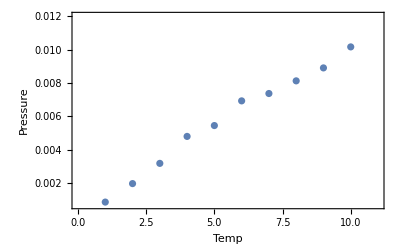

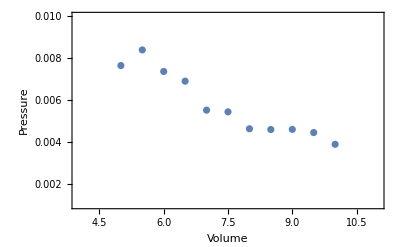

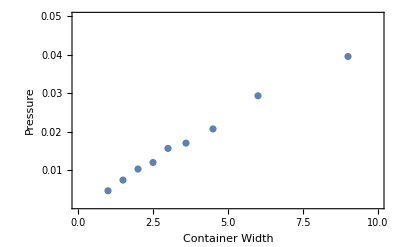

```mathematica
(*Shows the pressure as temperature changes (it has a constant volume of 10*10)*)ListPlot[constVolume,PlotRange ->{{0,11},{.0007,.012}}, Frame -> True, FrameLabel -> {"Temp", "Pressure"}]
(*Shows the pressure as Volume changes (it has a constant Temp of 4)*)
ListPlot[constTemp,PlotRange -> {{4,11},{.001,.01}}, Frame -> True, FrameLabel -> {"Volume", "Pressure"}]
(*Shows the pressure as the volume stays constant but the dimensions change.*)
ListPlot[dimXY,PlotRange -> {{0,10},{.001,.05}}, Frame -> True, FrameLabel -> {"Container Width", "Pressure"}]
```

0.56

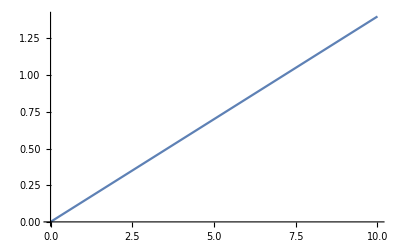

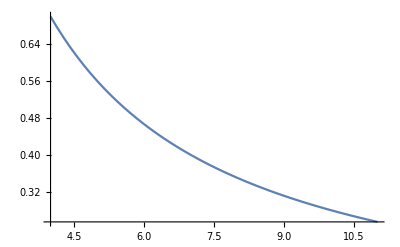

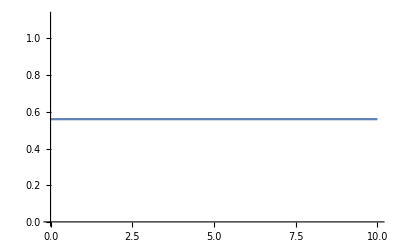

```mathematica
(*P=nrt/v*)
ConstVolumeFunc[T_]=100*0.007*T/5;
ConstTemperatureGraph[V_]=100*0.007*4/V;
ConstTempConstVol[x_]=100*0.007*4/5
Plot[ConstVolumeFunc[T],{T,0,10}]
Plot[ConstTemperatureGraph[V],{V,4,11}]
Plot[ConstTempConstVol[x],{x,0,10}]
```

### Notes for us

```mathematica
(*
NOTES for me
.1 m/s
10 m- wide
in one time step at most .1 m
so in 1000 time steps 100 m
take 100 time steps to go across box
t=dist/vel
t=10/.1=100 s
so each time step is 1 sec*)
(*timestep = 1sec
mass=1 kg
V=vel = .1 m/sec
dV=V-(-V)=2V
momentum=mass*dV
(momentum/time) = pressure
add up all dV for all of the molecules and all the masses  and then divide by time for the pressure*)
(*Pressure= force/bottom edge*)
```

```mathematica
box=Graphics[{Thick, Green, Rectangle[{0,-1},{2,1}]}];
ListAnimate[listOfGraphs];
```

```mathematica
getTotalEnergy[Temp_,NumberOfAtoms_]:=Module[{kb=0.005, totalVelocity=0},
totalVeolocity=Sqrt[3*NumberOfAtoms*Temp*(*mass of atom*)kb]
]
getSpeed[Energy_,numLeft_,origRatio_]:=Module[{magVel=0,xVel=0,yVel=0,theta=RandomReal[{0,2*Pi}],aproxDevide=Energy/numLeft,newEnergy=0,newNumLeft=0},
If[numLeft>1,
magVel=aproxDevide+RandomReal[{-aproxDevide*.1,aproxDevide*.1}];
(*If[,,];*)
newEnergy=Energy-magVel,
magVel=Energy];
newNumLeft=numLeft-1;

(*come up with a magnitude for the velocity*)
(*break it up into its x and y componants*)
xVel=magVel*Cos[theta];
yVel=magVel*Sin[theta];
{xVel,yVel,newEnergy}]
GenVelocityList[Temp_,Num_]:=Module[{TotsE=0,n=Num,sketchList={},VelList={}},
TotsE=getTotalEnergy[Temp,Num]//N;
sketchList={0,0,TotsE};
While[n>0,sketchList=getSpeed[sketchList[[3]],n,TotsE/100];VelList=Append[VelList,{sketchList[[1]],sketchList[[2]]}];(*Print[sketchList];*)n--];
VelList]
GenVelocityList[10,100]
```

Stuff to do:

Plot graph of our pressure
allow for change in momentum
const T:
const V: 5
change: 5-10  .5 step size